# Algebra of Invariants

## Prelude

We need to use some built-in and some self-written packages in order to define all necessary things for what is to come.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ShowStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
```

```mathematica
AppendTo[$Path,"~/Users/MatthewMaddock/Desktop/Birdtracks"];
<<NewProd033.m;
Needs["Fierz`"];
<<CFlat.m;
<<Utils.m;
<<SolveRules.m;
```

```mathematica
NewProd[YP,YScalarQ,Tr]
```

```mathematica
NewProd[NqP,NqScalarQ,Tr]
```

```mathematica
(*(NqScalarQ[#]=True)&/@{Subscript[c, _],Subscript[α, _,_]}*)
```

```mathematica
NewProd[UP,UscalarQ,Tr];
NewProd[PP,PPscalarQ,PPTr];
```

```mathematica
Needs["Notation`"];
```

```mathematica
Notation[Subscript[t, a_] ⟺ t[a_]];
Notation[Subscript[T, a_] ⟺ T[a_]];
Notation[Subscript[δ, a_,b_] ⟺ d[a_,b_]];
Notation[Subscript[δδ, a_,b_] ⟺ da[a_,b_]];

InfixNotation[⋄,PP];
InfixNotation[≀,YP];
(*InfixNotation[·,QP];*)
InfixNotation[∘,UP];
Notation[Subscript[1, a_] ⟺ Id[a_]]
```

```mathematica
SetOptions[Fierz,FierzProduct->UP,FierzTrace->Tr,FierzP->P,Fierzt->t,FierzN->Nc,FierzDelta->δ];
SetAttributes[δ,Orderless];

(PscalarQ[#]=True)&/@{Nc,Subscript[a,_]};
(PPscalarQ[#]=True)&/@{Nc,Subscript[cc,_],Subscript[a,_],Subscript[b,_],Subscript[aa,_],Subscript[bb,_]};(UscalarQ[#]=True)&/@{Nc};
```

```mathematica
(YScalarQ[#]=True)&/@{Nc,Subscript[a,_],n};
```

```mathematica
Clear[FixFactored];
FixFactored=(#/.(a_+b_)(a_+c_)/;Simplify[b+c]==0:>a^2-b^2)&;
```

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

## Graphical representations for δ-algebras

We define a function that is able to draw the primitive invariants, if given as δδ-products.

```mathematica
Clear[δToBirdTrack];

Options[δToBirdTrack]={Background->White,Delta->δδ,Scale->1};

δToBirdTrack[expr_,A_:a,B_:b,options___Rule]:=(*δToBirdTrack[expr,A,B,options]=*)Module[{l,s,aa,bb,res,hsep,vsep,samesep,bgcolor,delta,scale,m},
(* options *)

bgcolor:=Background/.{options}/.Options[δToBirdTrack];
delta:=Delta/.{options}/.Options[δToBirdTrack];
scale:=.02(Scale/.{options}/.Options[δToBirdTrack]);


hsep=5;
vsep=2;
samesep=hsep/6;

l=(expr//Cases[#,Subscript[A, i],Infinity,Heads->True]&//Union//Length);
h=l*vsep;
res=(expr/.delta[aa__]->m[Line[aa]]//.m[aa__]m[bb__]->m[aa,bb]);
midpoint[Subscript[aa_, i_],Subscript[bb_, j_]]:= ((pos[Subscript[aa, i]]+pos[Subscript[bb, j]])/2+If[aa===bb,1,0]If[aa===A,1,-1]{If[Abs[i-j]-1===0,-samesep,0]+.8*hsep,0});
pos[Subscript[B, i_]]={hsep/2 ,h/2-(i-1)vsep};
pos[Subscript[A, i_]]={-hsep/2,h/2-(i-1)vsep};
res//(#/.m[aa__]:>(m[aa]/. Line[ii_,jj_]->Line[pos[jj],midpoint[ii,jj],pos[ii]]))&//(#/.Line[aa__]:>{{Thickness[.1],bgcolor,BSplineCurve[{aa},SplineDegree->50]},{Arrowheads[{0,.21}],Arrow[BSplineCurve[{aa},SplineDegree->50],.45],BSplineCurve[{aa},SplineDegree->50]}})&//(#/.m[aa__]:>(Show[Graphics[{aa}],Background->bgcolor ,ImageSize->Scaled[scale]]))&


];
```

## Defining the Algebra and Product Vectors

Mathematica has a built-in way of dealing with permutations via the Combinatorica package. Using the intrinsic way in which the permutations of S_n, for a particular n, are ordered, one can define a permutation ρ via a coefficient vector
		ρ = (0,0,...,0,1,0,....,0),
where the 1 appears in the i^th place, and ρ is the i^th permutation in the intrinsic ordering. In order to then multiply permutations, when viewed as these coefficient vectors, one needs to define the product of the vectors using the intrinsic ordering of the permutations. This product is defined as Vprod.

```mathematica
Clear[SaveVprod,VprodFileName,LoadVprod]

VprodFileName[alg_[a__]]:={ToString[alg],ToString/@{a}}//Flatten//Riffle[#,"-"]&//StringJoin@@#&//(StringJoin@@{#,".m"})&;



SaveVprod[alg_]:=Module[{name=VprodFileName[alg]},Put[DefineVprod[alg],name];Print["Saving "<>ToString[alg]<>" to "<>FindFile[name]]]/;!FileExistsQ[VprodFileName[alg]]


LoadVprod[alg_]:=Module[{name=VprodFileName[alg]},Print["Loading "<>ToString[alg]<>" from "<>FindFile[name]];Vprod[alg][Table[Pattern[Evaluate[ToExpression["a"<>ToString[i]]],Blank[]],{i,Dimension[alg]}],Table[Pattern[Evaluate[ToExpression["b"<>ToString[i]]],Blank[]],{i,Dimension[alg]}]]=Get[name]];
```

```mathematica
(*VprodFileName[PermAlg[2]]
VprodFileName[PermAlg[5]]
VprodFileName[qqbAlg[2,3]]

Directory[]

FileNames["*.m"]
*)
```

```mathematica
(*Clear[Vprod,mVprod];*)

Vprod[alg_][a_List,b_List,c__List]:=Vprod[alg][Vprod[alg][a,b],c];
Vprod[alg_][a_List]=a;
```

Vprod for PermAlg[n]:

```mathematica
Clear[DefineVprod];

DefineVprod[alg_]:=Module[{},LoadVprod[alg]]/;FileExistsQ[VprodFileName[alg]]

Dimension[PermAlg[n_]]=n!;

DefineVprod[PermAlg[n_]]:=
Module[{res},res=DefineVprod[PermAlg[n]]=Vprod[PermAlg[n]][Table[Pattern[Evaluate[ToExpression["a"<>ToString[i]]],Blank[]],{i,Dimension[PermAlg[n]]}],Table[Pattern[Evaluate[ToExpression["b"<>ToString[i]]],Blank[]],{i,Dimension[PermAlg[n]]}]]=
Module[{c,i},
GroupMultiplicationTable[System`SymmetricGroup[n]]//Transpose//
Table[ToExpression["a"<>ToString[i]],{i,Dimension[PermAlg[n]]}].(#/.i_?IntegerQ->Subscript[c, i]).Table[ToExpression["b"<>ToString[i]],{i,Dimension[PermAlg[n]]}]&//Table[ShowStatus["Vprod component of PermAlg["<>ToString[n]<>"]:  "<>ToString[i]<>" of "<>ToString[Dimension[PermAlg[n]]]];Coefficient[#,Subscript[c, i]],{i,Dimension[PermAlg[n]]}]&];
SaveVprod[PermAlg[n]];
res
]
```

Warning: the Transpose in the above is a bit of a surprise -- the system is indeed reading things from left to right instead of right to left. This becomes visible for the first time at n=3, where things become non-commuting.

```mathematica
DefineVprod[PermAlg[2]]
(*SaveVprod[PermAlg[2]]*)

(*SaveVprod[PermAlg[2]]
LoadVprod[PermAlg[2]]
??Vprod*)
```

Loading PermAlg[2] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-2.m

{a1 b1+a2 b2,a2 b1+a1 b2}

```mathematica
DefineVprod[PermAlg[3]]
```

Loading PermAlg[3] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-3.m

{a1 b1+a2 b2+a3 b3+a5 b4+a4 b5+a6 b6,a2 b1+a1 b2+a5 b3+a3 b4+a6 b5+a4 b6,a3 b1+a4 b2+a1 b3+a6 b4+a2 b5+a5 b6,a4 b1+a3 b2+a6 b3+a1 b4+a5 b5+a2 b6,a5 b1+a6 b2+a2 b3+a4 b4+a1 b5+a3 b6,a6 b1+a5 b2+a4 b3+a2 b4+a3 b5+a1 b6}

```mathematica
DefineVprod[PermAlg[4]];
```

Loading PermAlg[4] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-4.m

```mathematica
DefineVprod[PermAlg[5]];
(*SaveVprod[PermAlg[5]]*)
```

Loading PermAlg[5] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-5.m

```mathematica
DefineVprod[PermAlg[6]];
(*SaveVprod[PermAlg[6]]*)
```

Loading PermAlg[6] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-6.m

## Permutation groups using the built-in facilities

### Preliminary explorations

```mathematica
(*NewProd[PP,PscalarQ,Tr];

PscalarQ[a_]:=True/;FreeQ[a,System`Cycles]*)
```

```mathematica
(*Permutations[Table[i,{i,3}]]//FindPermutation/@#&*)
```

```mathematica
(*GroupElements[System`SymmetricGroup[3]]*)
```

```mathematica
(*GroupElements[System`SymmetricGroup[3]]//(#.Table[Subscript[a, i],{i,#//Length}])&

PermutationProduct[%,System`Cycles[{{2,3}}]]

%//ExpandP[#,PermutationProduct]&*)
```

```mathematica
(*GroupElements[System`SymmetricGroup[2]]//(#.Table[Subscript[a, i],{i,#//Length}])&//PP[#,#]&//ExpandP[#,PP]&//(#/.PP->PermutationProduct)&//(#-System`Cycles[{}])&//Collect[#,_System`Cycles]&*)
```

```mathematica
(*GroupElements[System`SymmetricGroup[3]]//(#.Table[Subscript[a, i],{i,#//Length}])&//PP[#,#]&//ExpandP[#,PP]&//(#/.PP->PermutationProduct)&//Collect[#,_System`Cycles]&*)
```

```mathematica
(*GroupElements[System`SymmetricGroup[3]]

GroupElements[System`SymmetricGroup[4]]

Complement[%,%%]*)
```

```mathematica
(*{GroupElements[System`SymmetricGroup[3]],
System`Cycles[{{3,4}}]}//Flatten//PermutationGroup//GroupElements//Length*)
```

```mathematica
(*GroupMultiplicationTable[System`SymmetricGroup[3]];
%//MatrixForm
Table[Subscript[a, i],{i,3!}].(%%/.i_?IntegerQ->Subscript[c, i]).Table[Subscript[b, i],{i,3!}]//Table[Coefficient[#,Subscript[c, i]],{i,3!}]&*)
```

```mathematica
(*GroupMultiplicationTable[System`SymmetricGroup[6]]//(#/. 5->c/.i_?IntegerQ->0)&//Timing//#[[1]]&*)
```

```mathematica
(*GroupMultiplicationTable[System`SymmetricGroup[3]]//
Table[Subscript[a, i],{i,3!}].(#/.i_?IntegerQ->Subscript[c, i]).Table[Subscript[b, i],{i,3!}]&//Table[Coefficient[#,Subscript[c, i]],{i,3!}]&//Timing*)
```

### Defining the algebra and product vectors

```mathematica
Clear[SaveVprod,VprodFileName,LoadVprod]

VprodFileName[alg_[a__]]:={ToString[alg],ToString/@{a}}//Flatten//Riffle[#,"-"]&//StringJoin@@#&//(StringJoin@@{#,".m"})&;



SaveVprod[alg_]:=Module[{name=VprodFileName[alg]},Put[DefineVprod[alg],name];Print["Saving "<>ToString[alg]<>" to "<>FindFile[name]]]/;!FileExistsQ[VprodFileName[alg]]


LoadVprod[alg_]:=Module[{name=VprodFileName[alg]},Print["Loading "<>ToString[alg]<>" from "<>FindFile[name]];Vprod[alg][Table[Pattern[Evaluate[ToExpression["a"<>ToString[i]]],Blank[]],{i,Dimension[alg]}],Table[Pattern[Evaluate[ToExpression["b"<>ToString[i]]],Blank[]],{i,Dimension[alg]}]]=Get[name]];
```

```mathematica
VprodFileName[PermAlg[2]]
VprodFileName[qqbAlg[2,3]]

Directory[]

FileNames["*.m"]
```

PermAlg-2.m

qqbAlg-2-3.m

/Users/MatthewMaddock/Desktop/December_work/Mathematica/Birdtracks

{Birdtracks_package.m,CFlat.m,Fierz.m,InvariantAlgebra.m,MOLDOperators.m,NewProd033.m,PermAlg-2.m,PermAlg-3.m,PermAlg-4.m,PermAlg-5.m,PermAlg-6.m,qqbAlg-2-1.m,SolveRules.m,Utils.m}

```mathematica
(*Clear[Vprod,mVprod];*)

Vprod[alg_][a_List,b_List,c__List]:=Vprod[alg][Vprod[alg][a,b],c];
Vprod[alg_][a_List]=a;
```

Vprod for PermAlg[n]:

```mathematica
Clear[DefineVprod];

DefineVprod[alg_]:=Module[{},LoadVprod[alg]]/;FileExistsQ[VprodFileName[alg]]

Dimension[PermAlg[n_]]=n!;

DefineVprod[PermAlg[n_]]:=
Module[{res},res=DefineVprod[PermAlg[n]]=Vprod[PermAlg[n]][Table[Pattern[Evaluate[ToExpression["a"<>ToString[i]]],Blank[]],{i,Dimension[PermAlg[n]]}],Table[Pattern[Evaluate[ToExpression["b"<>ToString[i]]],Blank[]],{i,Dimension[PermAlg[n]]}]]=
Module[{c,i},
GroupMultiplicationTable[System`SymmetricGroup[n]]//Transpose//
Table[ToExpression["a"<>ToString[i]],{i,Dimension[PermAlg[n]]}].(#/.i_?IntegerQ->Subscript[c, i]).Table[ToExpression["b"<>ToString[i]],{i,Dimension[PermAlg[n]]}]&//Table[ShowStatus["Vprod component of PermAlg["<>ToString[n]<>"]:  "<>ToString[i]<>" of "<>ToString[Dimension[PermAlg[n]]]];Coefficient[#,Subscript[c, i]],{i,Dimension[PermAlg[n]]}]&];
SaveVprod[PermAlg[n]];
res
]
```

Warning: The transpose of the multiplication table here is a bit of a surprise! The built in function Permute and the multiplication table are defined as a right action, which is not how we want to do things!

```mathematica
DefineVprod[PermAlg[2]]
(*SaveVprod[PermAlg[2]]*)

(*SaveVprod[PermAlg[2]]
LoadVprod[PermAlg[2]]
??Vprod*)
```

Loading PermAlg[2] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-2.m

{a1 b1+a2 b2,a2 b1+a1 b2}

```mathematica
GroupMultiplicationTable[System`SymmetricGroup[3]]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6
2 | 1 | 4 | 3 | 6 | 5
3 | 5 | 1 | 6 | 2 | 4
4 | 6 | 2 | 5 | 1 | 3
5 | 3 | 6 | 1 | 4 | 2
6 | 4 | 5 | 2 | 3 | 1)

```mathematica
DefineVprod[PermAlg[3]]
```

Loading PermAlg[3] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-3.m

{a1 b1+a2 b2+a3 b3+a5 b4+a4 b5+a6 b6,a2 b1+a1 b2+a5 b3+a3 b4+a6 b5+a4 b6,a3 b1+a4 b2+a1 b3+a6 b4+a2 b5+a5 b6,a4 b1+a3 b2+a6 b3+a1 b4+a5 b5+a2 b6,a5 b1+a6 b2+a2 b3+a4 b4+a1 b5+a3 b6,a6 b1+a5 b2+a4 b3+a2 b4+a3 b5+a1 b6}

```mathematica
DefineVprod[PermAlg[6]];
(*SaveVprod[PermAlg[6]]*)
```

Loading PermAlg[6] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-6.m

### Cycle-Notation into Kronecker-δδ-Notation

The following translates Mathematica’s Cycles into Kronecker δδ-products:

```mathematica
Clear[PermutationToExplicit,CyclesToExplicit,OneCyclesToExplicit];

CyclesToExplicit[System`Cycles[{}],___]=1;

CyclesToExplicit[System`Cycles[aa:{__List}],A_:a,B_:b]:=Module[{},
aa//{#,RotateRight[#]}&/@#&//Transpose/@#&//Flatten[#,1]&//Product[δδ[Subscript[A, #[[i,1]]],Subscript[B, #[[i,2]]]],{i,#//Length}]&]

OneCyclesToExplicit[OneCycles[aa_List],A_:a,B_:b]:=Product[δδ[Subscript[A, aa[[i]]],Subscript[B, aa[[i]]]],{i,aa//Length}]

PermutationToExplicit[PermAlg[n_],A_:a,B_:b][expr_]:=Module[{},
(* find all omitted 1-cycles *)expr//(#/.System`Cycles[aa_]:>OneCycles[Complement[Table[i,{i,n}],aa//Flatten//Union]]System`Cycles[aa])&//(#/.aa_OneCycles:>OneCyclesToExplicit[aa,A,B]/.aa_System`Cycles:>CyclesToExplicit[aa,A,B])&
]
```

```mathematica
System`Cycles[{{1,4},{2,3}}]//CyclesToExplicit//δToBirdTrack

System`Cycles[{{1,3,2,4}}]//CyclesToExplicit//δToBirdTrack

System`Cycles[{{1,2,3,4}}]//CyclesToExplicit//δToBirdTrack

System`Cycles[{{1,4},{2,3}}]//PermutationToExplicit[PermAlg[6]]//δToBirdTrack

System`Cycles[{{1,4},{6,3}}]//PermutationToExplicit[PermAlg[6]]//δToBirdTrack

(*PermutationToExplicit[PermAlg[n_]]:=*)
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[ExplicitList];
ExplicitList[PermAlg[n_],A_:a,B_:b]:=(*ExplicitList[PermAlg[n],A,B]=*)GroupElements[System`SymmetricGroup[n]]//PermutationToExplicit[PermAlg[n],A,B]
```

```mathematica
(*ExplicitList[PermAlg[4]]
%//δToBirdTrack*)
```

```mathematica
ExplicitList[PermAlg[3]]//δToBirdTrack
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
??ExplicitToVec
```

## Algebras with qn quarks and qbn antiquarks

We now define mixed algebras V^(\otime qn)\(otimes(V^*))^(\otimes qbn).

```mathematica
Dimension[qqbAlg[qn_,qbn_]]=(qn+qbn)!;
ExplicitList[qqbAlg[qn_,qbn_],A_:a,B_:b]:=(*ExplicitList[qqbAlg[qn,qbn],A_,B_]=*)GroupElements[System`SymmetricGroup[qn+qbn]]//PermutationToExplicit[PermAlg[qn+qbn],A,B]//Swap[#,{Table[Subscript[A, i],{i,qn+1,qn+qbn}],Table[Subscript[B, i],{i,qn+1,qn+qbn}]}]&
```

```mathematica
ExplicitList[qqbAlg[2,1]]
%//δToBirdTrack
```

{δδ[a_1,b_1] δδ[a_2,b_2] δδ[b_3,a_3],δδ[a_1,b_1] δδ[a_2,a_3] δδ[b_3,b_2],δδ[a_1,b_2] δδ[a_2,b_1] δδ[b_3,a_3],δδ[a_1,a_3] δδ[a_2,b_1] δδ[b_3,b_2],δδ[a_1,b_2] δδ[a_2,a_3] δδ[b_3,b_1],δδ[a_1,a_3] δδ[a_2,b_2] δδ[b_3,b_1]}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ExplicitToVec[alg_,A_:a,B_:b][expr_]:=Table[Coefficient[expr,ExplicitList[alg,A,B]⟦i⟧],{i,Dimension[alg]}]

(*AbstractAlgList[qqbAlg[qn_,qbn_]]:=Table[Subscript[qqbAlg[qn,qbn], i],{i,Dimension[qqbAlg[qn,qbn]]}]

ExplicitToAbstractAlg[qqbAlg[qn_,qbn_,A_:a,B_:b]][expr_]:=expr/.Table[ExplicitList[qqbAlg[qn,qbn],A,B][[i]]->Subscript[qqbAlg[qn,qbn], i],{i,Dimension[qqbAlg[qn,qbn]]}];*)

(*
ExplicitToVec[qqbAlg[qn_,qbn_],A_:a,B_:b][expr_]:=Table[Coefficient[expr,ExplicitList[qqbAlg[qn,qbn],A,B][[i]]],{i,Dimension[qqbAlg[qn,qbn]]}];*)
```

```mathematica
(*Table[ExplicitList[qqbAlg[qn,qbn],a,c]ExplicitList[qqbAlg[qn,qbn],c,b],{i,Dimension[qqbAlg[qn,qbn]]},{j,Dimension[qqbAlg[qn,qbn]]}]//(#//.δδ[aa_,Subscript[c, i_]]δδ[Subscript[c, i_],cc_]->δδ[aa,cc])&//(#/.δδ[a_,a_]->Nc)&*)


(*//δToBirdTrack//MatrixForm*)
```

In order to multiply permutations an linear combinations thereof, we need to define a product of the coefficient vectors

```mathematica
(*Clear[DefineVprod,Vprod];*)

DefineVprod[qqbAlg[qn_,qbn_]]:=(*DefineVprod[qqbAlg[qn,qbn]]=*)
Module[{res},
res=DefineVprod[qqbAlg[qn,qbn]]=Vprod[qqbAlg[qn,qbn]][Table[Pattern[Evaluate[ToExpression["a"<>ToString[i]]],Blank[]],{i,Dimension[qqbAlg[qn,qbn]]}],Table[Pattern[Evaluate[ToExpression["b"<>ToString[i]]],Blank[]],{i,Dimension[qqbAlg[qn,qbn]]}]]=
Module[{aa,bb,i},
aa=Table[ToExpression["a"<>ToString[i]],{i,Dimension[qqbAlg[qn,qbn]]}];
bb=Table[ToExpression["b"<>ToString[i]],{i,Dimension[qqbAlg[qn,qbn]]}];
(*
GroupMultiplicationTable[System`SymmetricGroup[n]]//
Table[Subscript[a, i],{i,Dimension[qqbAlg[qn,qbn]]}].(#/.i_?IntegerQ->Subscript[c, i]).Table[Subscript[b, i],{i,Dimension[qqbAlg[qn,qbn]]}]&//Table[ShowStatus["Vprod component of PermAlg["<>ToString[n]<>"]:  "<>ToString[i]<>" of "<>ToString[Dimension[qqbAlg[qn,qbn]]]];Coefficient[#,Subscript[c, i]],{i,Dimension[qqbAlg[qn,qbn]]}]&*)
Print["working"];
aa.Table[ShowStatus["Vprod: multiplying basis elements of qqbAlg["<>ToString[qn]<>","<>ToString[qbn]<>"]:  "<>ToString[i]<>"x"<>ToString[j]<>" of "<>ToString[Dimension[qqbAlg[qn,qbn]]]<>" squared"];ExplicitList[qqbAlg[qn,qbn],a,c][[i]]ExplicitList[qqbAlg[qn,qbn],c,b][[j]]//(#//.δδ[aaa_,Subscript[c, i_]]δδ[Subscript[c, i_],cc_]->δδ[aaa,cc])&//(#/.δδ[aaa_,aaa_]->Nc)&,{i,Dimension[qqbAlg[qn,qbn]]},{j,Dimension[qqbAlg[qn,qbn]]}].bb//Expand//Table[ShowStatus["Vprod: retrieving component of qqbAlg["<>ToString[qn]<>","<>ToString[qbn]<>"]:  "<>ToString[i]<>" of "<>ToString[Dimension[qqbAlg[qn,qbn]]]];Coefficient[#,ExplicitList[qqbAlg[qn,qbn]][[i]]],{i,Dimension[qqbAlg[qn,qbn]]}]&

];

SaveVprod[qqbAlg[qn,qbn]];
(*Print["saved"];*)
res
]
```

```mathematica
(*ExplicitList[qqbAlg[3,3],a,c]*)
DefineVprod[qqbAlg[2,1]]
(*DefineVprod[qqbAlg[2,2]]*)
(*SaveVprod[qqbAlg[2,2]]*)
```

Loading qqbAlg[2, 1] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/qqbAlg-2-1.m

{a1 b1+a3 b3,a2 b1+a1 b2+a5 b2+a5 b3+a2 b4+a3 b4+a2 b2 Nc+a5 b4 Nc,a3 b1+a1 b3,a4 b1+a3 b2+a6 b2+a6 b3+a1 b4+a4 b4+a4 b2 Nc+a6 b4 Nc,a5 b1+a2 b3+a1 b5+a5 b5+a2 b6+a3 b6+a2 b5 Nc+a5 b6 Nc,a6 b1+a4 b3+a3 b5+a6 b5+a1 b6+a4 b6+a4 b5 Nc+a6 b6 Nc}

```mathematica
(*DefineVprod[qqbAlg[4,1]]*)
(*SaveVprod[qqbAlg[4,1]]*)
```

```mathematica
(*DefineVprod[qqbAlg[1,1]]*)
(*SaveVprod[qqbAlg[1,1]]*)
```

## Hermitean Young Projection Operators as Coefficient Vectors

### Symmetrizers and antisymmetrizers using built in mathematica functions

First, we need to define Symmetrizers and Anti-symmetrizers. We do this in th following way: Mathematica has a built in way of dealing with Permutations (System`Cycles). A (anti-) symmetrizer may thus be written as
		S = ∑_i  a_i ρ_i,
where the ρ_i are permutations and a_i are the coefficients of these permutations (many of which will be zero). We may thus define the (anti-) symmetrizer by its coefficient vector, where the ρ_i are ordered as Mathematica does so intrinsically.

However, we first need to define the signature of a permutation.

```mathematica
Clear[CycleSig];
CycleSig[expr_System`Cycles]:=expr//(#/.System`Cylces[{}]->1/.System`Cycles[a__]:>Times@@(a//(-1)^(Length[#]+1)&/@#&))&
```

We are now able to define the coefficient vectors corresponding to symmetrizers and anti-symmetrizers.

```mathematica
Clear[SymmetrizerVec,AntiSymmetrizerVec];
SymmetrizerVec[{aa__?IntegerQ},n_]:=Module[{alts=Alternatives@@Complement[Table[i,{i,n!}],{aa}],a},
GroupElements[System`SymmetricGroup[n]]//(#/.System`Cycles[a__]:>0/;!FreeQ[a,alts])&//(#/.a_System`Cycles-> 1)&//#/(Length[{aa}]!)&]

AntiSymmetrizerVec[{aa__?IntegerQ},n_]:=Module[{alts=Alternatives@@Complement[Table[i,{i,n!}],{aa}],a},
GroupElements[System`SymmetricGroup[n]]//(#/.System`Cycles[a__]:>0/;!FreeQ[a,alts])&//(#/.a_System`Cycles-> CycleSig[a])&//#/(Length[{aa}]!)&]
```

```mathematica
(*
DefineVprod[PermAlg[4]];
(*SaveVprod[PermAlg[4]]*)
SymmetrizerVec[{1,3,4},4]
%//Vprod[PermAlg[4]][#,#]&
AntiSymmetrizerVec[{1,4},4]

DefineVprod[PermAlg[3]];SaveVprod[PermAlg[3]];
AntiSymmetrizerVec[{1,2,3},3]
*)
```

### Young Projection Operators

A Young projection operator is the product (using the previously defined Vprod) of symmetrizers and anti-symmetrizers. However, for it to be idempotent, an additional constant is usually required. The below functions take care of the normalization of a (Young) projection operator.

```mathematica
Clear[normalizeProjectorVec,normalizationFactorVec];
normalizationFactorVec[alg_][cand_]:=Module[{norm},(Vprod[alg][cand,cand]norm- cand)//Simplify//(#/. 0->Sequence[])&//Union//(#[[1]]==0)&//Solve[#,norm][[1,1,2]]&]

normalizeProjectorVec[alg_][cand_]:=Module[{norm},(Vprod[alg][cand,cand]norm- cand)//Simplify//(#/. 0->Sequence[])&//Union//(#[[1]]==0)&//Solve[#,norm][[1,1,2]]&//(# cand)&]
```

We can once again define a Young projection operator as the coefficient vector of the permutations. This is done in the following Definition.

```mathematica
Clear[YoungProjectorVec];

YoungProjectorVec[tableau_,n_]:=Module[{syms,asyms,cand,norm},(*
Print[" tablau in: ",tableau];*)
syms=tableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[SymmetrizerVec[#[[i]],n],{i,#//Length}]&//(#/.{}:>{Table[If[i==1,1,0],{i,n!}]})&;
asyms=tableau//TransposeTableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[AntiSymmetrizerVec[#[[i]],n],{i,#//Length}]&//(#/.{}:>{Table[If[i==1,1,0],{i,n!}]})&;

(*Print["syms: ",syms," asyms: ",asyms];*)

(* unnormalized Young projector *)
cand=Vprod[PermAlg[n]][Vprod[PermAlg[n]]@@syms,Vprod[PermAlg[n]]@@asyms];

(*Print[" cand: ",cand];*)

(* supplying the normalization and output *)
(Vprod[PermAlg[n]][cand,cand]norm- cand)//Simplify//(#/. 0->Sequence[])&//Union//(#[[1]]==0)&//Solve[#,norm][[1,1,2]]&//(# cand)&
]
```

### Young Tableaux and Parent Tableaux

We now define a function that gives all Young tableaux of n boxes, YTableaux[n]. Thereafter, we define a function that produces the parent tableau of a particular Young tableau

```mathematica
Clear[YTableaux,YTableauBlocks];
YTableauBlocks[n_]:=YTableauBlocks[n]=IntegerPartitions[n]//Tableaux/@#&
YTableaux[n_]:=Tableaux[n];(*YTableaux[n]=YTableauBlocks[n]//Flatten[#,1]&*)
```

```mathematica
YTableauGroups[5]//TableauGrid/@#&/@#&
```

YTableauGroups[5]

```mathematica
YTableauGroups[5]Invarient
```

Invarient YTableauGroups[5]

```mathematica
Clear[ParentYoungTableau];
ParentYoungTableau[tableau_]:=tableau/.(tableau//Flatten//Sort//Last)->Sequence[]/.{}->Sequence[];
```

### KS Hermitean Young Projection Operaotrs

Now this is ready to implement the KS iterative formula. The termination condition will be the case of two:

```mathematica
Clear[KSHermiteanYoungProjectorVec,PairTableaux,TableauOf,KSParentYoungProjectorVec];

PairTableaux=IntegerPartitions[2]//Tableaux/@#&//Flatten[#,1]&;

KSHermiteanYoungProjectorVec[{{1,2}},n_]:=KSHermiteanYoungProjectorVec[{{1,2}},n]=Module[{res},
res=YoungProjectorVec[{{1,2}},n];
KSParentYoungProjectorVec[res]=res;
TableauOf[res]={{1,2}};
res
];

KSHermiteanYoungProjectorVec[{{1},{2}},n_]:=KSHermiteanYoungProjectorVec[{{1},{2}},n]=Module[{res},
res=YoungProjectorVec[{{1},{2}},n];
KSParentYoungProjectorVec[res]=res;
TableauOf[res]={{1},{2}};
res
];
`~~~~~~
KSHermiteanYoungProjectorVec[tableau_,n_]:=(*HermiteanYoungProjectorVec[tableau,n]=*)Module[{res},
res=Vprod[PermAlg[n]][KSHermiteanYoungProjectorVec[ParentYoungTableau[tableau],n],YoungProjectorVec[tableau,n],KSHermiteanYoungProjectorVec[ParentYoungTableau[tableau],n]];
KSParentYoungProjectorVec[res]=KSHermiteanYoungProjectorVec[ParentYoungTableau[tableau],n];
TableauOf[res]=tableau;
res];
```

From the theory, we know that the KS Operators are Hermitean. However, in order to confirm this, we need to compare the KS operators with their Hermitean conjugate. To this end, we define the function HermiteanConjugateVec, which forms the Hermitean Conjugate coefficient vector of some other coefficient vector.

```mathematica
Clear[HermiteanConjugateVec,hermiteanVecQ];

DefineHermiteanConjugateVec[alg_]:=HermiteanConjugateVec[alg][Table[Pattern[Evaluate[ToExpression["a"<>ToString[i]]],Blank[]],{i,Dimension[alg]}]]=ExplicitList[alg].Table[ToExpression["a"<>ToString[i]],{i,Dimension[alg]}]//Swap[#,{a,b}]&//(#/.a_δδ:>Reverse[a])&//Table[Coefficient[#,ExplicitList[alg][[j]]],{j,Dimension[alg]}]&;

HermiteanConjugationMatrix[alg_]:=HermiteanConjugationMatrix[alg]=Module[{a},HermiteanConjugateVec[alg][Table[Subscript[a, i],{i,Dimension[alg]}]]//Table[Coefficient[#,Subscript[a, i]],{i,Dimension[alg]}]&]

hermiteanVecQ[alg_][vec_]:=(HermiteanConjugateVec[alg][vec]-vec)//Simplify//Union//(#=={0})&

DefineHermiteanConjugateVec[PermAlg[4]]

HermiteanConjugateVec[PermAlg[4]]

HermiteanConjugationMatrix[PermAlg[4]]//MatrixForm
%//Tr
```

{a1,a2,a3,a5,a4,a6,a7,a8,a13,a19,a14,a20,a9,a11,a15,a21,a17,a23,a10,a12,a16,a22,a18,a24}

HermiteanConjugateVec[PermAlg[4]]

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

10

```mathematica
HermiteanConjugateVec[PermAlg[4]]
```

HermiteanConjugateVec[PermAlg[4]]

```mathematica
HermiteanConjugateVec[PermAlg[4]]
```

HermiteanConjugateVec[PermAlg[4]]

```mathematica
HermiteanConjugateVec[PermAlg[4]]
```

HermiteanConjugateVec[PermAlg[4]]

### Short KS Hermitean Young Projecetion Operaotrs

We found that there is a shortened version of the Hermitean Young projection operators: Instead of multiplying the Hermitean parent on either side, it is sufficient to form a chain of ancester Young projection operators. We thus need to define the tableau ancestry, TableauAncestry, and then build the shorter Hermitean Young projection operators from there, HermiteanYoungProjectionVec.

```mathematica
Clear[HermiteanYoungProjectorVec,TableauAncestry];

(*TableauAncestry[tableaux_List]=tableaux/;(Last[tableaux]//Flatten//Length)≤2*)
TableauAncestry[tableau_]:=Module[{res={tableau},length=tableau//Flatten//Length},
(*Print[length];*)
While[(Last[res]//Flatten//Length)>2,
AppendTo[res,Last[res]//ParentYoungTableau]];
res
]

HermiteanYoungProjectorVec[tableau_,n_]:=Module[{m=tableau//Flatten//Length,ta,res},
ta=TableauAncestry[tableau]//YoungProjectorVec[#,n]&/@#&;
res=Vprod[PermAlg[n]][Sequence@@Drop[Reverse[ta],-1],Sequence@@ta];
TableauOf[res]=tableau;
res
]
```

As an example, we construct all hermitean Young projection oeprators as coefficient vectors for the 4q-algebra.

```mathematica
DefineVprod[PermAlg[4]];
YTableaux[4][[2]]
%//TableauAncestry

YTableaux[4]//HermiteanYoungProjectorVec[#,4]&/@#&

%//(Vprod[PermAlg[4]][#,#]-#)&/@#&

%%//(HermiteanConjugateVec[PermAlg[4]][#]-#)&/@#&

%%%//MultipletDimension[PermAlg[4]]/@#&
```

Loading PermAlg[4] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-4.m

{{1,3,4},{2}}

{{{1,3,4},{2}},{{1,3},{2}},{{1},{2}}}

{{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/8,1/8,1/16,1/16,1/16,1/16,-1/8,-1/8,-1/16,-1/16,-1/16,-1/16,-1/16,-1/16,1/16,1/16,0,0,-1/16,-1/16,1/16,1/16,0,0},{1/8,1/24,-1/16,-1/48,-1/48,5/48,1/8,1/24,-1/16,-1/48,-1/48,5/48,-1/16,-1/48,-1/16,-1/48,-1/12,-1/12,-1/48,5/48,-1/48,5/48,-1/12,-1/12},{1/8,-1/24,1/8,-1/24,-1/24,-1/24,1/8,-1/24,1/8,-1/24,-1/24,-1/24,1/8,-1/24,1/8,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24},{1/12,-1/12,1/24,-1/24,-1/24,1/24,-1/12,1/12,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,1/12,-1/12,1/24,-1/24,-1/24,1/24,-1/12,1/12},{1/12,1/12,-1/24,-1/24,-1/24,-1/24,1/12,1/12,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,1/12,1/12,-1/24,-1/24,-1/24,-1/24,1/12,1/12},{1/8,1/24,-1/8,-1/24,-1/24,1/24,-1/8,-1/24,1/8,1/24,1/24,-1/24,1/8,1/24,-1/8,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24},{1/8,-1/24,1/16,-1/48,-1/48,-5/48,-1/8,1/24,-1/16,1/48,1/48,5/48,-1/16,1/48,1/16,-1/48,-1/12,1/12,1/48,5/48,-1/48,-5/48,1/12,-1/12},{1/8,-1/8,-1/16,1/16,1/16,-1/16,1/8,-1/8,-1/16,1/16,1/16,-1/16,-1/16,1/16,-1/16,1/16,0,0,1/16,-1/16,1/16,-1/16,0,0},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{1/24 Nc (1+Nc) (2+Nc) (3+Nc),1/8 (-1+Nc) Nc (1+Nc) (2+Nc),1/8 (-1+Nc) Nc (1+Nc) (2+Nc),1/8 (-1+Nc) Nc (1+Nc) (2+Nc),1/12 (-1+Nc) Nc^2 (1+Nc),1/12 (-1+Nc) Nc^2 (1+Nc),1/8 (-2+Nc) (-1+Nc) Nc (1+Nc),1/8 (-2+Nc) (-1+Nc) Nc (1+Nc),1/8 (-2+Nc) (-1+Nc) Nc (1+Nc),1/24 (-3+Nc) (-2+Nc) (-1+Nc) Nc}

As another example, we calculate the Hermitean Young projection vectors for the 3q-algebra.

```mathematica
DefineVprod[PermAlg[3]];DefineHermiteanConjugateVec[PermAlg[3]];

YTableaux[3]//TableauGrid/@#&
YTableaux[3]//HermiteanYoungProjectorVec[#,3]&/@#&

%//(Vprod[PermAlg[3]][#,#]-#)&/@#&

%%//(HermiteanConjugateVec[PermAlg[3]][#]-#)&/@#&
%%%//MultipletDimension[PermAlg[3]]/@#&
```

Loading PermAlg[3] from /Users/MatthewMaddock/eclipse-workspace/Birdtracks/PermAlg-3.m

{1 | 2 | 3,1 | 3
2 | ,1 | 2
3 | ,1
2
3}

{{1/6,1/6,1/6,1/6,1/6,1/6},{1/3,1/6,-1/3,-1/6,-1/6,1/6},{1/3,-1/6,1/3,-1/6,-1/6,-1/6},{1/6,-1/6,-1/6,1/6,1/6,-1/6}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{1/6 Nc (1+Nc) (2+Nc),1/3 (-1+Nc) Nc (1+Nc),1/3 (-1+Nc) Nc (1+Nc),1/6 (-2+Nc) (-1+Nc) Nc}

Defining the ist of ll Projection operators for the 3q-algebra as PermAlgProjList[3]. However, this is unnecessary, given the definition we provde in TransisiontElements.nb

```mathematica
(*IntegerPartitions[3]//Tableaux/@#&//Flatten[#,1]&
PermAlgProjList[3]=%//HermiteanYoungProjectorVec[#,3]&/@#&*)
```

```mathematica
(*DefineVprod[PermAlg[6]];*)
```

```mathematica
(*IntegerPartitions[6]//Tableaux/@#&//Flatten[#,1]&//HermiteanYoungProjectorVec[#,6]&/@#&;
%//Plus@@#&
%%//Length*)

(*%%//Table[Vprod[PermAlg[5]][#[[i]],#[[j]]],{i,#//Length},{j,#//Length}]&*)
```

### Dimensions of Irreps coresponding to certain Multiplets

```mathematica
Clear[MultipletDimension];

MultipletDimension[alg_][projvec_]:=projvec.ExplicitList[alg]//(#/.b->a)&//(#//.δδ[aaa_,Subscript[a, i_]]δδ[Subscript[a, i_],cc_]->δδ[aaa,cc])&//(#/.δδ[aaa_,aaa_]->Nc)&//Factor;
```

An Example - not sure what

```mathematica
ExplicitList[PermAlg[4]]//Swap[#,{a,b}]&//(#/.a_δδ:>Reverse[a])&//Table[Coefficient[#[[i]],ExplicitList[PermAlg[4]][[j]]],{i,#//Length},{j,#//Length}]&//Tr
```

10

## Drawing Young Tableaux

The following function draws a list of lists as a Young tableau

```mathematica
Clear[TableauGrid];

TableauGrid=Module[{pos},
pos=#//Position[#,_?IntegerQ]&//Rule[#,True]&/@#&;
Magnify[Grid[#,Frame->{None,None,pos},ItemStyle->Directive[FontSize->12,FontFamily->Times],Spacings->{0,0}(*,ItemSize->Scaled[.2,.2]*)],1]]&;
```

As an example, we draw all Young tableaux consisting of 4 Boxes

```mathematica
YTableaux[4]//TableauGrid/@#&
```

{1 | 2 | 3 | 4,1 | 3 | 4
2 |  | ,1 | 2 | 4
3 |  | ,1 | 2 | 3
4 |  | ,1 | 3
2 | 4,1 | 2
3 | 4,1 | 4
2 | 
3 | ,1 | 3
2 | 
4 | ,1 | 2
3 | 
4 | ,1
2
3
4}

We can determine the dimension of the irreducible representation corresponding to a particular (Hermitean) Young projection operator. The following function MultipletDimension gives this representation, provided the algebra is specified by measn of the first input.

## Formal Young Projectors and Birdtracks

### Writing (Hermitean) Young Projection Operators as Products of Symmetrizers and Anti-Symmetrizers

#### Young Operators

We have defined (Hermitean) Young proejction operators as coefficient vectors. While this allows us to use built-in Mthematica functions to perform calculations, it is not very easy to see what is going on, since we are more used to the symmetrizer and anti-symemtrizer notation. We now do this, writing for exampel a symmetrizer over indices 1,2 and 3 as
		S[{1,2,3}]
and an anti-symmetrizer over indices 1,3,4 and 6 as
		AS[{1,3,4,6}].
We then wrap the function YP around it, to let Mathematica know that it is a special product, not the regular built-in product for scalars. This prevents Mathematica from apllying the properties of the regular product (such as commutativity) on YP, as they do not hold in general

```mathematica
Clear[formYoungProjector];

formYoungProjector[tableau_]:=Module[{syms,asyms,cand,norm},(*
Print[" tablau in: ",tableau];*)
syms=tableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[S[#[[i]]],{i,#//Length}]&;
asyms=tableau//TransposeTableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[AS[#[[i]]],{i,#//Length}]&;

(*Print["syms: ",syms," asyms: ",asyms];*)

(* unnormalized Young projector *)
cand=Join[syms,asyms]//YP@@#&;

(*Print[" cand: ",cand];*)

(* supplying the normalization and output *)
(*(Vprod[PermAlg[n]][cand,cand]norm- cand)//Simplify//(#/. 0->Sequence[])&//Union//(#[[1]]==0)&//Solve[#,norm][[1,1,2]]&//(# cand)&*)
cand
]
```

For example, the Young projection operators of the 3q-algebra become.

```mathematica
YTableaux[3]//TableauGrid/@#&
YTableaux[3]//formYoungProjector/@#&
```

{1 | 2 | 3,1 | 3
2 | ,1 | 2
3 | ,1
2
3}

{YP[S[{1,2,3}]],S[{1,3}]≀AS[{1,2}],S[{1,2}]≀AS[{1,3}],YP[AS[{1,2,3}]]}

#### Shortened KS-Operators

We can also play this game for the Hermitean Young projection operators, and write them in terms of S and AS. The following gives the shortened KS-operators

```mathematica
Clear[formHermiteanYoungProjector];

formHermiteanYoungProjector[tableau_]:=Module[{},
(*Print["rowordered"];*)
formYoungProjector[tableau]//YP[#,Reverse[#]]&
]/;OrderedQ[RowWord[tableau]]


formHermiteanYoungProjector[tableau_]:=Module[{},
(*Print["columnordered"];*)
formYoungProjector[tableau]//YP[Reverse[#],#]&
]/;OrderedQ[ColumnWord[tableau]]

(*TableauAncestry[tableaux_List]=tableaux/;(Last[tableaux]//Flatten//Length)≤2*)
(*TableauAncestry[tableau_]:=Module[{res={tableau},length=tableau//Flatten//Length},
(*Print[length];*)
While[(Last[res]//Flatten//Length)>2,
AppendTo[res,Last[res]//ParentYoungTableau]];
res
]*)


formHermiteanYoungProjector[tableau_]:=Module[{m=tableau//Flatten//Length,ta},
ta=TableauAncestry[tableau]//formYoungProjector[#]&/@#&;
YP[Sequence@@Drop[Reverse[ta],-1],Sequence@@ta]
]
```

#### KS-Operators

We can also write the full KS-operators as products of symemtrizers and anti-symmetrizers.

```mathematica
Clear[KSformHermiteanYoungProjector,KSformParentYoungProjector];

KSformHermiteanYoungProjector[{{1,2}}]:=KSformHermiteanYoungProjectorVec[{{1,2}}]=Module[{res},
res=formYoungProjector[{{1,2}}];
KSformParentYoungProjector[res]=res;
TableauOf[res]={{1,2}};
res
];

KSformHermiteanYoungProjector[{{1},{2}}]:=KSformHermiteanYoungProjector[{{1},{2}}]=Module[{res},
res=formYoungProjector[{{1},{2}}];
KSformParentYoungProjector[res]=res;
TableauOf[res]={{1},{2}};
res
];

KSformHermiteanYoungProjector[{{1,2}}]

KSformHermiteanYoungProjector[{{1},{2}}]

KSformHermiteanYoungProjector[tableau_]:=(*HermiteanYoungProjectorVec[tableau,n]=*)Module[{res},
res=YP[KSformHermiteanYoungProjector[ParentYoungTableau[tableau]],formYoungProjector[tableau],KSformHermiteanYoungProjector[ParentYoungTableau[tableau]]];
(*ParentYoungProjectorVec[res]=HermiteanYoungProjectorVec[ParentYoungTableau[tableau],n];*)
TableauOf[res]=tableau;
res];
```

YP[S[{1,2}]]

YP[AS[{1,2}]]

```mathematica
YP[S[{1,2}]]
```

YP[S[{1,2}]]

An example

S[{1,2}]≀AS[{1,3}]≀T[S[{1,2}],S[{3,4}]]≀T[AS[{1,3}],AS[{2,4}]]≀S[{1,2}]≀AS[{1,3}]≀S[{1,2}]

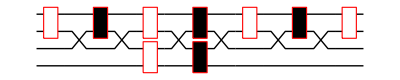

```mathematica
{{1,2},{3,4}}//KSformHermiteanYoungProjector//simplifyFormHermiteanYoungProjector
%//graphicalYP
```

### Simplification Rules

We have found various ways of simplifying these Hermitean Young projection operators (which lead to the MOLD-operators, programmed in MOLDOPerators.nb). These simplification rules can be implimented in Mathematica by means of replacement rules.

Also, in the below, we have lumped non-overlapping symmetrizers into a function T, and similarly with non-overlapping anti-symmetrizer. For example
		YP[S[{1,2}],S[{3,4}]] -> YP[T[S[{1,2}],S[{3,4}]]].
At this point, this function T is completely unnecessary. However, in a later section, we define the function graphycalYP, which draws the operators as birdtracks. graphycalYP knows that it can draw symmetrizers (resp. anti-symmetrizers) as boxes directly on top of each other, if the function T is wrapped around them.

```mathematica
Clear[simplifyFormHermiteanYoungProjector,simplifyT];

(*Clear[T];Attributes[T]={};*)
Clear[sortT];sortT=(#/.a_T:>Sort[a,#1[[1,1]]<#2[[1,1]]&])&;

(*SetAttributes[T,Orderless];*)
(*T[a__]:=Sort[T[a],#1[[1,1]]<#2[[1,1]]&]/;!OrderedQ[T[a],#1[[1,1]]<#2[[1,1]]&]*)
(*T[a_]=a;*)
```

```mathematica
simplifyFormHermiteanYoungProjector[expr_]:=expr//(#/.YP[a___,aa_,aa_,b___]->YP[a,aa,b])&//(#//.YP[a___,A_[aa_List],A_[bb_List],b___]:>YP[a,A[Union[aa,bb]],b]/;Intersection[aa,bb]===aa||Intersection[aa,bb]===bb)&//(#/.YP[a_]->a)&//(#//.YP[a___,A_[aa_List],B_[cc_List],A_[bb_List],B_[dd_List],b___]:>YP[a,A[aa],B[dd],b]/;Union[aa,bb]===aa&&Intersection[aa,bb]===bb&&Union[cc,dd]===dd&&Intersection[cc,dd]===cc)&//(#//.YP[a___,A_[c_List],A_[cc_List],b___]:>YP[a,T[A[c],A[cc]]//sortT,b]/;Intersection[c,cc]==={})&//(#//.YP[a___,aa:T[c__],bb:(S|AS)[cc_List],b___]:>YP[a,T[c,bb]//sortT,b]/;Intersection[(aa/.(S|AS->Identity))//List@@#&//Flatten,cc]==={})&
(*(#//.YP[a___,aa:(S|AS)[c_List],bb:(S|AS)[cc_List],b___]:>YP[a,T[aa,bb],b]/;Intersection[c,cc]==={})&//(#//.YP[a___,aa:T[c__],bb:(S|AS)[cc_List],b___]:>YP[a,T[c,bb],b]/;Intersection[(aa/.(S|AS->Identity))//List@@#&//Flatten,cc]==={})&*)

simplifyT[expr_]:=expr//(#//.YP[a___,T[b___,A_[aa_List],c___],A_[bb_List],d___]:>YP[a,T[b,c],A[bb],d]/;Union[aa,bb]==bb&&Intersection[aa,bb]==aa)&//(#//.YP[a___,A_[bb_List],T[b___,A_[aa_List],c___],d___]:>YP[a,A[bb],T[b,c],d]/;Union[aa,bb]==bb&&Intersection[aa,bb]==aa)&//(#//.YP[a___,T[aa___],T[bb___],T[aa___],T[bb___],d___]:>YP[a,T[aa],T[bb],d])&//(#//.YP[x___,T[a___,A_[aa_List],b___],T[c___,B_[cc_List],d___],T[a___,A_[bb_List],b___],T[c___,B_[dd_List],d___],xx___]:>YP[x,T[a,A[aa],b],T[c,B[dd],d],xx]/;Union[aa,bb]===aa&&Intersection[aa,bb]===bb&&Union[cc,dd]===dd&&Intersection[cc,dd]===cc)&//(#//.YP[x___,T[a___,A_[aa_List],b___],B_[cc_List],A_[bb_List],B_[dd_List],xx___]:>YP[x,T[a,A[aa],b],B[dd],xx]/;Union[aa,bb]===aa&&Intersection[aa,bb]===bb&&Union[cc,dd]===dd&&Intersection[cc,dd]===cc)&//(#//.YP[x___,A_[aa_List],B_[cc_List],A_[bb_List],T[a___,B_[dd_List],b___],xx___]:>YP[x,A[aa],T[a,B[dd],b],xx]/;Union[aa,bb]===aa&&Intersection[aa,bb]===bb&&Union[cc,dd]===dd&&Intersection[cc,dd]===cc)&//(#//.YP[x___,T[a___,A_[aa_List],b___],T[a___,A_[bb_List],b___],xx___]:>YP[x,T[a,A[aa],b],xx]/;Union[aa,bb]==aa&&Intersection[aa,bb]==bb)&//(#//.YP[x___,T[a___,A_[aa_List],b___],T[a___,A_[bb_List],b___],xx___]:>YP[x,T[a,A[bb],b],xx]/;Union[aa,bb]==bb&&Intersection[aa,bb]==aa)&//(#//.T[]:>Sequence[])&//(#//.{YP[x___,T[a___,A_,b___],T[aa___,A_,bb___],xx___]:>YP[x,T[a,b],T[aa,A,bb],xx],T[]->Sequence[]})&//(#//.T[a_]:>a)&//(#//.YP[a___,aa:T[c__],bb:(S|AS)[cc_List],b___]:>YP[a,T[c,bb],b]/;Intersection[(aa/.(S|AS->Identity))//List@@#&//Flatten,cc]==={})&//sortT
```

#### More Simplification Rules - Nowhere used

```mathematica
Clear[simplifyYP,simplifyYPStep,simplifyYPRules];
simplifyYP=FixedPoint[(#//simplifyYPStep)&,#]&;
simplifyYPStep[expr_]:=expr//.simplifyYPRules;simplifyYPRules={YP[a___,A_[aa_List],A_[bb_List],b___]:>YP[a,A[Union[aa,bb]],b]/;(Intersection[aa,bb]===aa||Intersection[aa,bb]===bb) (* 1: absorb shorter S or AS in longer ones *),
YP[a___,A_[c_List],A_[cc_List],b___]:>YP[a,T[A[c],A[cc]]//sortT,b]/;Intersection[c,cc]==={} (* 2: pile commuting S|AS into "towers" T *),
YP[a___,A_[aa_List],T[bb__],b___]:> YP[a,T[bb,A[aa]]//sortT,b]/;Intersection[argContent[YP[bb]],aa]==={} 
(* 3a: absorb into existing T *),YP[a___,T[bb__],A_[aa_List],b___]:> YP[a,T[bb,A[aa]]//sortT,b]/;Intersection[argContent[YP[bb]],aa]==={} 
(* 3b: absorb into existing T *),YP[a___,T[b___,A_[aa_List],c___],A_[bb_List],d___]:>YP[a,T[b,c],A[bb],d]/;Union[aa,bb]==bb&&Intersection[aa,bb]==aa (* remove an entry from T *),YP[a___,A_[bb_List],T[b___,A_[aa_List],c___],d___]:>YP[a,A[bb],T[b,c],d]/;Union[aa,bb]==bb&&Intersection[aa,bb]==aa (* remove an entry from T opposite side *),
YP[x___,T[a___,A_[aa_List],b___],T[c___,B_[cc_List],d___],T[a___,A_[bb_List],b___],T[c___,B_[dd_List],d___],xx___]:>YP[x,T[a,A[aa],b],T[c,B[dd],d],xx]/;Union[aa,bb]===aa&&Intersection[aa,bb]===bb&&Union[cc,dd]===dd&&Intersection[cc,dd]===cc (* 4 T simplifications *)
(*YP[x___,T[a___,A_[aa_List],b___],T[a___,A_[bb_List],b___],xx___]:>YP[x,T[a,A[aa],b],xx]/;Union[aa,bb]==aa&&Intersection[aa,bb]==bb (* analogue of 1 for T *),
YP[x___,T[a___,A_,b___],T[aa___,A_,bb___],xx___]:>YP[x,T[a,b],T[aa,A,bb],xx] *)(* 3: cancel S|AS between adjacent T. Needs upgrade to 1 *)
};

Clear[commuteCancel,commuteCancelRule,argContent];
argContent[expr_YP]:=(expr/.S|AS|T->Sequence)//List@@#&//Flatten//Union;
commuteCancelRule={YP[x___,A_[aa_List],c___,A_[bb_List],y___]:>YP[x,c,A[bb],y]/;(Intersection[aa,bb]===aa&&(Intersection[argContent[YP[c]],aa]=={})),
YP[x___,A_[aa_List],c___,A_[bb_List],y___]:>YP[x,A[aa],c,y]/;(Intersection[aa,bb]===bb&&(Intersection[argContent[YP[c]],bb]=={})) }
```

{x___≀A_[aa_List]≀c___≀A_[bb_List]≀y___:>x≀c≀A[bb]≀y/;aa∩bb===aa&&argContent[YP[c]]∩aa=={},x___≀A_[aa_List]≀c___≀A_[bb_List]≀y___:>x≀A[aa]≀c≀y/;aa∩bb===bb&&argContent[YP[c]]∩bb=={}}

### Product of S and AS to Coefficient Vector - IMPORTANT

The following function takes an operator defined as a product of S and AS, and turns it into a coefficient vector.

```mathematica
Clear[yPToVec];
yPToVec[alg_][expr_]:=Module[{n=Plus@@alg},
(expr/.T[a__]->Sequence[a]/.{S[a_]->SymmetrizerVec[a,n],AS[a_]->AntiSymmetrizerVec[a,n]})//YP//Vprod[alg]@@#&
];
```

The following is an example for the 6q-algebra. It is commented out since it gives a very long outcome

```mathematica
(*YTableaux[6][[(YTableaux[6]//Length)-19]]
%//formHermiteanYoungProjector//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&
%//graphicalYP

%%//yPToVec[PermAlg[6]];
(*%//normalizeProjectorVec[PermAlg[6]];*)
%//hermiteanVecQ[PermAlg[6]]*)
```

The following function removes the T again. However, this is nowhere used

```mathematica
Clear[tContent];
tContent[a_T]:=List@@(a//.S|AS->Sequence)//Flatten
T[S[{1,4}],S[{2,5}],S[{3,6}]]//tContent
```

{1,4,2,5,3,6}

This builds a list of line numbers with line numbers in S or AS listed first, filled out with the missing ones up to n.

```mathematica
Clear[symmOrder];
symmOrder[n_][A:(S|AS)[a_List]]:=Module[{},
(*Print["symmOrder on S|AS ",A];*)
order=Join[Table[i,{i,a[[1]]-1}],a]//Join[#,Sort[Complement[Table[i,{i,n}],#]]]&
];

symmOrder[n_][T[a__]]:=Module[{aa},
aa=(T[a]/.(S|AS->Identity))//List@@#&//Flatten;

(*Print["symmOrder on T aa ",aa];*)
order=Join[Table[i,{i,aa[[1]]-1}],aa]//Join[#,Sort[Complement[Table[i,{i,n}],#]]]&;
(*Print["symmOrder on T order ",order];*)
order
];
```

An example.

```mathematica
T[S[{1,3}],S[{4,5}]]//symmOrder[5]
```

{1,3,4,5,2}

### Writing Operators as Birdtracks - Graphical Notations

The following function graphicalYP draws the birdtrack corresponding to particular operators. It takes the prodct YP and draws the functions S, AS and T[a___] accordingly.

```mathematica
Clear[graphicalYP];

Options[graphicalYP]={Background->White,Scale->1};

graphicalYP[expr_YP,options___Rule]:=Module[{max=(expr/.S|AS->Identity/.YP->List/.T->List)//Flatten//Max,order,type,symset,width,hsep,vsep,samesep,(*h,*)bgcolor,scale},

bgcolor:=Background/.{options}/.Options[graphicalYP];
scale:=40(Scale/.{options}/.Options[graphicalYP]);
(*Print[scale,bgcolor];*)

hsep=5/2;
vsep=-3;
samesep=hsep/6;
(*h=max*vsep;*)

(*Print["max ",max];
Print[expr];*)
order=expr//(#/. A_T:>symmOrder[max][A])&//(#/. A:(S|AS)[a_List]:>symmOrder[max][A])&//List@@#&;
type=expr//(#/. A:(S|AS)[a_List]:>Head[A]/.S->White/.AS->Black)&//List@@#&;
symset=expr//(#/. A:(S|AS)[a_List]->a)&//List@@#&;

(*Print["order: ",order];Print["type ",type];Print["symset ",symset];*)

(* width will depend on ordered or not *)
width=order//If[OrderedQ[#],2hsep,5hsep]&/@#&;
(*PrependTo[width,0];*)
(*Print[width//N];*)
width=Table[width[[i]]/2+Sum[width[[k]],{k,i-1}],{i,width//Length}];
(*Print[width//N];*)

(* now build lines for each of the factors *)

Table[If[OrderedQ[order[[i]]],
(*lines=Table[Line[{{-hsep, order[[i,j]] vsep},{hsep,order[[i,j]]vsep}}],{j,max}],
lines=Table[Line[{{-2.5hsep,j vsep},{-2hsep,j vsep},{-hsep, order[[i,j]] vsep},{hsep,order[[i,j]]vsep},{2hsep ,j vsep},{2.5hsep ,j vsep}}],
{j,max}]*)
lines=Table[Line[{{-hsep, order[[i,j]] vsep},{hsep,order[[i,j]]vsep}}],{j,max}],
lines=Table[Line[{{-2.5hsep,order[[i,j]] vsep},{-2hsep,order[[i,j]] vsep},{-hsep, j vsep},{hsep,j vsep},{2hsep ,order[[i,j]] vsep},{2.5hsep ,order[[i,j]] vsep}}],
{j,max}]
]//{#,{EdgeForm[{Thin,Red}],If[Head[type[[i]]]===T,
Table[(*Print[symset[[i,k,1]]];*){type[[i,k]],Rectangle[{-.5hsep,(Position[order[[i]],symset[[i,k,1]]][[1,1]] -.4)vsep},{.5hsep,(Position[order[[i]],symset[[i,k,1]]][[1,1]]+Length[symset[[i,k]]]-1+.4)vsep}]},{k,type[[i]]//Length}]
,{type[[i]],Rectangle[{-.5hsep,(symset[[i,1]] -.4)vsep},{.5hsep,(symset[[i,1]]+Length[symset[[i]]]-1+.4)vsep}]}]}}&//Translate[#,{width[[i]],0}]&//Graphics,
{i,order//Length}
]//Show[#,Background->bgcolor ,ImageSize->{Automatic,scale}]&

]

graphicalYP[expr:(_S|_AS|_T),options___Rule]:=graphicalYP[YP[expr],options];
```

An example - selected Young tableaux of 6 boxes

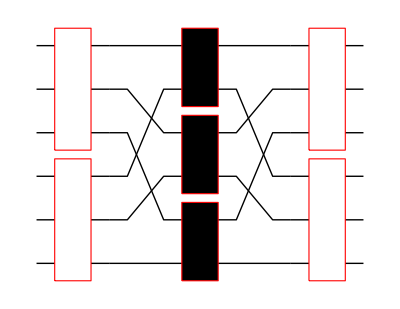
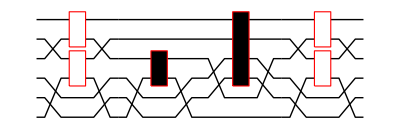
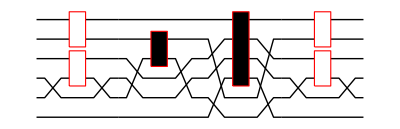
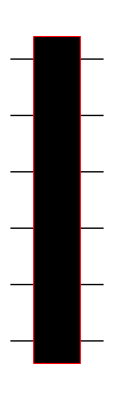

```mathematica
threeantiquarkstab={{{1,2,3},{4,5,6}},{{1,3},{2,6},{4},{5}},{{1,2},{3,5},{4},{6}},{{1},{2},{3},{4},{5},{6}}};
%//formHermiteanYoungProjector/@#&;
%//simplifyFormHermiteanYoungProjector//simplifyT;
%//graphicalYP/@#&
```

### Fix Hermitean Appearance

Unlike the MOLD-operators, the birdtracks corresponding to the above defined Hermitean Young projection operators may not look Hermitean. to rectify this, we define the function fixHermiteanAppearance.

```mathematica
Clear[fixHermiteanAppearanceYP];

fixHermiteanAppearanceYP[expr_]:=expr/;(Simplify[expr-Reverse[expr]]==0);
fixHermiteanAppearanceYP[expr_]:=Module[{rev=Reverse[expr],l=Length[expr]},
YP@@Table[FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,YP[expr[[i]],rev[[i]]]],{i,l}]//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&
];
```

As an example, consider the Hermitean Young projection operators of the 6q-algebra. This example is commented out, as it needs a long time to run

```mathematica
(*YTableaux[6];
%//TableauGrid/@#&
%%//formHermiteanYoungProjector/@#&;
%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&;
%//graphicalYP/@#&
%%//fixHermiteanAppearanceYP/@#&;
%//graphicalYP/@#&*)


(*DefineVprod[PermAlg[6]];
YTableaux[6][[(YTableaux[6]//Length)-16]]
(*YTableaux[6][[1]]*)
%//formHermiteanYoungProjector;
%//graphicalYP;
%%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&
%//graphicalYP
(*%%//yPToVec[PermAlg[6]];
%//hermiteanVecQ[PermAlg[6]]*)
%%//fixHermiteanAppearanceYP//(#/.simplifyYPRules)&
%//(#/.a_YP:>graphicalYP[a])&
%%//(normalizationFactorVec[PermAlg[6]][yPToVec[PermAlg[6]][#]]#)&
%//(#/.a_YP:>graphicalYP[a])&*)


(*myproj[6]=%//(normalizationFactorVec[PermAlg[6]][yPToVec[PermAlg[6]][#]]#)&/@#&;
%//(#/.a_YP:>graphicalYP[a]/.A:(S|AS)[a_]:>graphicalYP[A])&
(*%//yPToVec[PermAlg[6]]/@#&;*)
(*%//hermiteanVecQ[PermAlg[6]]/@#&*)*)


(*myproj[6]//(#/.a_YP ->1/._S|_AS->1)&//If[IntegerQ[#],ToString[#],"\\frac{"<>ToString[Numerator[#]]<>"}{"<>ToString[Denominator[#]]<>"}"]&/@#&//(#/."1"->"")&(*//Table[Put[#[[i]],"normP6-"<>ToString[i]<>".tex"],{i,#//Length}]&*)*)


(*myproj[6][[2]]//(#/.a_YP:>yPToVec[PermAlg[6]][a])&//(Vprod[PermAlg[6]][#,#]-#)&
*)


(*myproj[6]//(#/.a_YP:>yPToVec[PermAlg[6]][a]/.A:(S|AS)[a_]:>yPToVec[PermAlg[6]][A])&//(#.ExplicitList[PermAlg[6]])&//(#/.b->a)&//(#//.δδ[aaa_,Subscript[a, i_]]δδ[Subscript[a, i_],cc_]->δδ[aaa,cc])&//(#/.δδ[aaa_,aaa_]->Nc)&//Factor*)
```

### Drawing Operators of the 3q-Algebra - An Example

We draw the Hermtiean Young Projection operators for the 3q-algebra. The version marked as myproj[3] already has the appropriate normalization factors incorporated

{1 | 2 | 3,1 | 3
2 | ,1 | 2
3 | ,1
2
3}

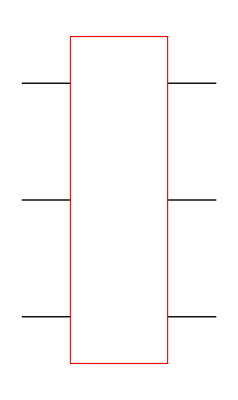
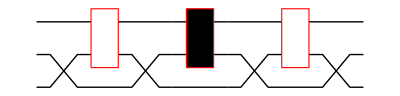
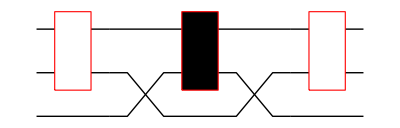
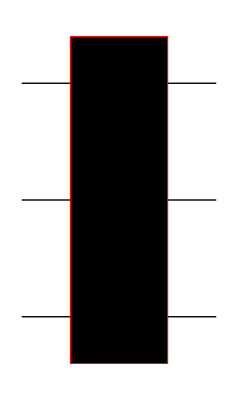

{-Graphics-,(4 -Graphics-)/3,(4 -Graphics-)/3,-Graphics-}

```mathematica
YTableaux[3];
%//TableauGrid/@#&
%%//formHermiteanYoungProjector/@#&;
%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&;
%//graphicalYP/@#&
%%//fixHermiteanAppearanceYP/@#&;
(*%//graphicalYP/@#&*)
myproj[3]=%//(normalizationFactorVec[PermAlg[6]][yPToVec[PermAlg[6]][#]]#)&/@#&;
%//(#/.a_YP:>graphicalYP[a]/.A:(S|AS)[a_]:>graphicalYP[A])&
```